### Variables:

All units are SI

```mathematica
ϵInP=12.5; (*Dielectric constant of InP*)
e=1.6*10^-19;
c=3*10^8;
λ=1550*10^-9;
h=6.626*10^-34;
ϵ0=8.85*10^-12;
L=20*10^-6; (*length of the sensing region in meters*)
w=4*10^-6;(*Width of the waveguide in meters*)
wfiber=4*10^-6;
Δt=0.001; (*This is the sensing time*)
η=1; (*Quantum efficiency*)
n=3.36; (*Refractive index of the InP core at 1550nm.*)
a=500*10^-9; (*Thickness of the waveguide in meters*)
b=10*10^-9; (*Approximate width of charge modulation region. This is approximate: for b<<a, the solution is independent of b.*)
CecmInP=5.6*10^-21; (*This is the parameter that determines the strength of the free carrier effect in InP, in cm^3*)
CeInP=CecmInP*0.01^3; (*This is in m^3*)

ChargeCentroid =2.4219*10^-9;(*in meters. This was derived from simulations for silicon with 10^17/cm^3 doping.*)
```

### Figure 2 bottom:

```mathematica
Δn=n √(1/(Δt η P/(h c/λ)))
```

3.80504×10^-8 √(1/P)

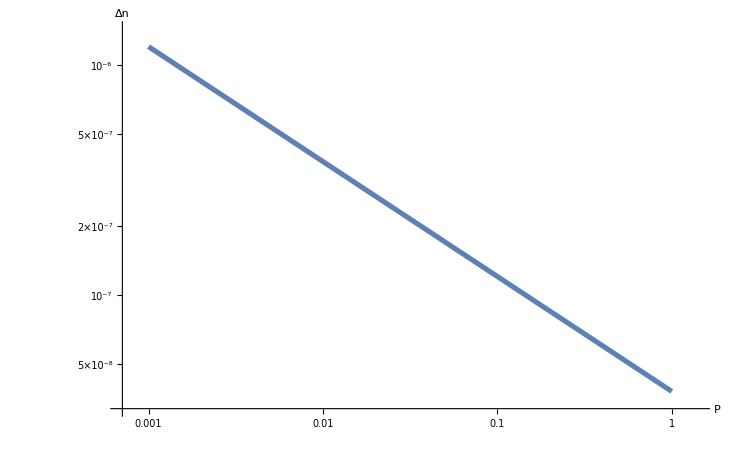

```mathematica
LogLogPlot[Δn,{P,0.001,1},AxesLabel->{"P","Δn"},AxesStyle->Large,PlotStyle->Thickness[.005]]
```

### Figure 3A

Calculating the total capacitance, with the insulating capacitor, interface capacitor, and depletion region capacitor in series:

```mathematica
A=w*L; (*Area of the nanosheet capacitor*)
(*Insulating Cap: ϵ0 ϵ A/d*)
InsulatingCap=ϵ0 A ϵoverd;
(*Interface Cap*)
InterfaceCap=1*wfiber*L//N;(*1 farad per square meter capacitance at fiber surface*)
DepletionRegionCap=w*L*ϵ0*ϵInP/ChargeCentroid;
Cap=1/(1/InsulatingCap+1/InterfaceCap+1/DepletionRegionCap); (*Effective capacitance*)
```

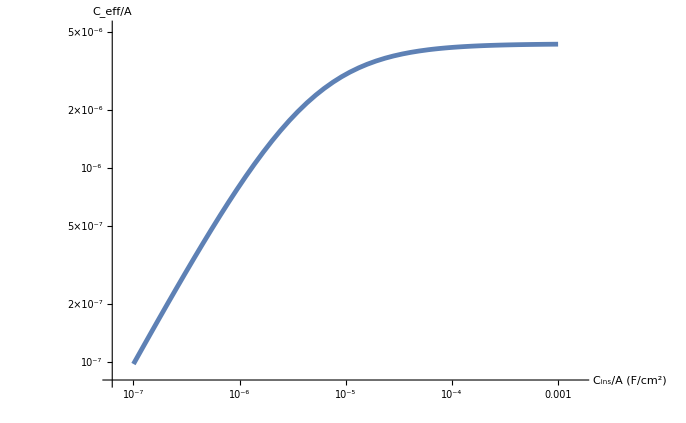

```mathematica
ϵoverd=CperA*10000/ϵ0; (*Defining the ratio ϵ/d in terms of the capacitance per unit area*)
LogLogPlot[Cap/(L*w*10000(*10000 is necessary to convert from m^-2 to cm^-2*)),{CperA,10^-7,.001},AxesLabel->{"C_ins/A (F/cm^2)","C_eff/A"},AxesStyle->Large,PlotStyle->Thickness[.005]]
```

### Figure 3B

This is equation 16 in the text

```mathematica
Δneff=CeInP b/(a+b) Cap/(e A b)ΔV;
```

We now solve equation 8 from the text to get the minimum ΔV that can be sensed:

```mathematica
Sol2=Solve[Δneff/n==√(1/(Δt η Pow/(h c/λ))),{ΔV}];
```

{{ΔV→4.4356×10^-17 (2.86161×10^11+(1.25×10^6)/CperA) √(1/Pow)}}

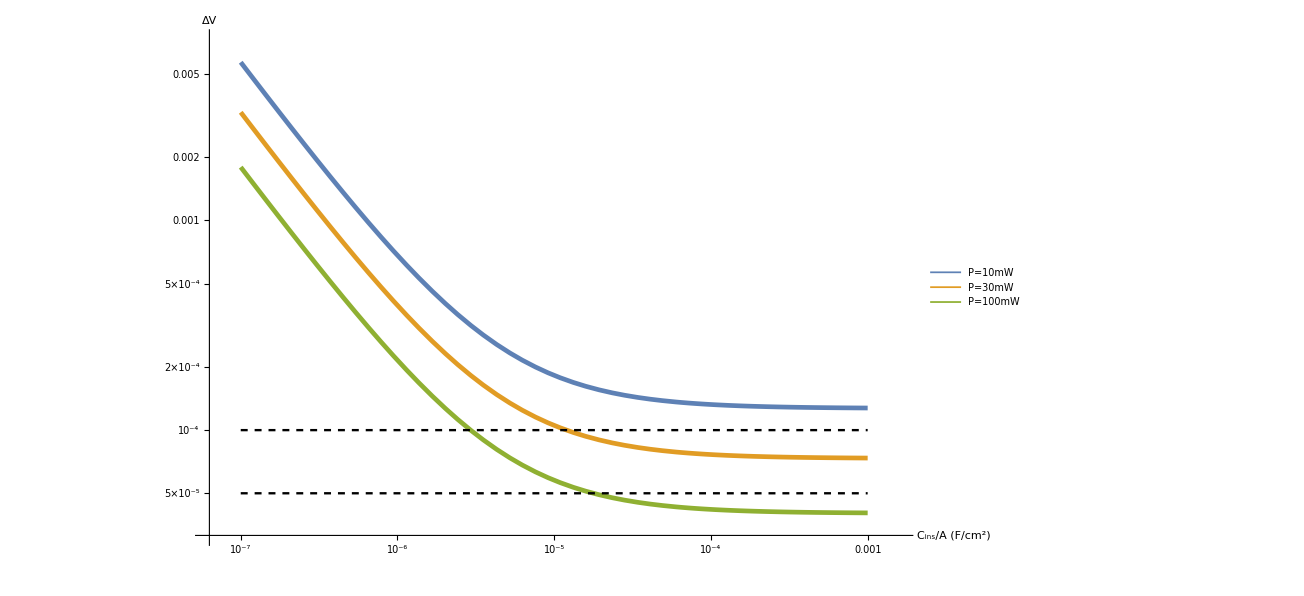

```mathematica
LogLogPlot[{ΔV/.Sol2/.{Pow->0.01},ΔV/.Sol2/.{Pow->0.03},ΔV/.Sol2/.{Pow->0.1},5*10^-5,10^-4},{CperA,10^-7,.001},AxesLabel->{"C_ins/A (F/cm^2)","ΔV"},AxesStyle->Large,PlotStyle->{Thickness[.0035],Thickness[.0035],Thickness[.0035],{Thickness[.00175],Black,Dashed},{Thickness[.00175],Black,Dashed}},PlotLegends->Placed[{"P=10mW","P=30mW","P=100mW"},{0.9,0.9}],Ticks->{Automatic,{{10^-6,"10^-6"},{3*10^-6,"3 x 10^-6"},{10^-5,"10^-5"},{3*10^-5,"3 x 10^-5"},{10^-4,"10^-4"},{3*10^-4,"3 x 10^-4"},{10^-3,"10^-3"},{3*10^-3,"3 x 10^-3"},{10^-2,"10^-2"}}}]
```